# Data Visualisation Lecture 1 - Beginnings

a.moura@abdn.ac.uk

## Introduction and motivation

Consider the world population from 1900 to the present time.

```mathematica
years={1900,1910,1920,1930,1940,1950,1960,
	1970,1980,1990,2000,2010,2020};
worldPop = {1.62*^9,1.74*^9,1.86*^9,2.04*^9,
	2.26*^9,2.52*^9,3.03*^9,3.7*^9,4.46*^9,
	5.33*^9,6.15*^9,6.96*^9,7.66*^9};
```

This data can be presented in a straightforward way as a spreadsheet:

```mathematica
Grid[Transpose[{Join[{"year"},years], 
	Join[{"population"},worldPop]}],Frame->All]
```

year | population
1900 | 1.62×10^9
1910 | 1.74×10^9
1920 | 1.86×10^9
1930 | 2.04×10^9
1940 | 2.26×10^9
1950 | 2.52×10^9
1960 | 3.03×10^9
1970 | 3.7×10^9
1980 | 4.46×10^9
1990 | 5.33×10^9
2000 | 6.15×10^9
2010 | 6.96×10^9
2020 | 7.66×10^9

Compare this with this graphical representation of the exact same data:

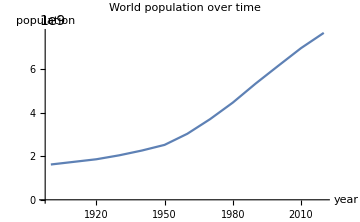

```mathematica
ListLinePlot[Transpose[{years,worldPop}],ImageSize->Medium,
	AxesLabel->{"year","population"},
	PlotLabel->"World population over time"]
```

We get a much better sense of how fast the world population has increased in the past 120 years from the plot, in a way that inspecting a list of numbers just does not convey. Upon inspecting the plot, it is immediately clear that the increase in population accelerated suddenly around the 1950s - something that is far from obvious when you inspect the data directly.

In general, graphs convey quantitative data to us in a much more immediate and visceral way than tables of numbers. Large parts of our brain are dedicated to processing visual input, and to a large extent, we reason using images. As a consequence, data visualisation is one of the most powerful ways to analyse and communicate data.

The goal of this course is to teach you how to use data visualisation effectively. More precisely:

You will learn what kinds of graphs are appropriate for different data;

You will learn how to find hidden patterns in data, and test hypotheses, by choosing the appropriate graphical representation;

You will learn how to craft graphs so that they tell a story, and make a point, and are maximally effective in communicating and convincing others.

We will do all this by using Mathematica. Having the power of a fully-fledged programming language allows us total freedom to customise graphs in any way we want; we can even create entirely new kinds of plots from scratch, if we need to. In addition, plots in Mathematica are not confined to being static entities: we can make them come alive, and turn plots into mini-apps that respond to inputs in many ways. In this course, you will master Mathematica’s data visualisation capabilities.

## Exploratory versus Explanatory data visualisation

When you are trying to make sense of some data, trying to understand why different quantities behave as they do, and how they are related to each other, you are exploring data. For example, suppose you have a dataset of economic measures such as GDP for various countries. You may speculate that a country’s wealth and its literacy rate go together: wealthy countries should have higher literacy rates on average. How do you test this hypothesis? What kind of plot would you make to see if this is true? This is exploring the data, and what you are doing is exploratory data visualisation.

On the other hand, suppose you finished your exploration, and you have convinced yourself that literacy is indeed strongly correlated with wealth. You now want to convince other people of that, through a presentation, or a publication. What plot is the most compelling and powerful in conveying this point? This will be a very different plot from those you used while you were exploring the data. When you are trying to communicate data to other people, you are doing explanatory data visualisation.

Both kinds of data visualisation will be covered in this course. The first half of the course will be dedicated to learning Mathematica’s graphics system in depth, and creating effective graphs for exploring many different kinds of data. In second half of the course, you will learn the fundamental principles of explanatory data visualisation and how to apply them to create graphs that effectively communicate data.

## The toolbox: the most useful plots

There are countless kinds of graphs, but most are specialised graphs that are only useful within a narrow discipline or area. A few graphs are universally useful, though. In fact, most of the time the graphs that you plot will be one of these kinds. They make up the fundamental toolbox of data visualisation:

Bar charts

Scatter plots

Line plots

We will introduce each of these plots in the following.

### Bar charts

Bar charts are the instrument of choice when you want to compare quantities in a dataset organised around categories. The term “category” here means discrete entities that are not reducible to numbers. For example, countries are one category, because they are well-defined entities, and one cannot fully define a country by using a number or set of numbers. The same is true for tropical diseases: malaria and yellow fever are not quantitative concepts; they cannot be reduced to numbers. On the other hand, “temperature” and “speed” are reducible to numbers, and do not define categories in the sense used here.

Of course, a country has many quantities associated with it: population, GDP, literacy rate, etc. We often want to visually compare some quantity - population, for example - across different countries. In cases like this, bar charts are usually what you want.

The basic form of the bar chart plot in Mathematica is illustrated below:

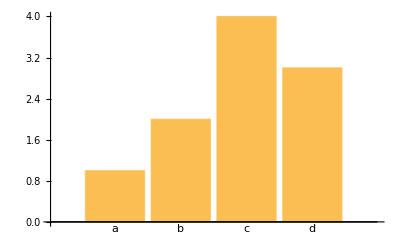

```mathematica
BarChart[{1,2,4,3},ChartLabels->{"a", "b", "c","d"}]
```

To focus on a more interesting example, let us get some data on the current population of a few countries.

```mathematica
CountryData["Brazil","Population"]
```

211049519 people

```mathematica
CountryData["UnitedKingdom","Name"]
```

United Kingdom

```mathematica
countriesM={"UnitedKingdom","UnitedStates","Brazil",
	"SouthAfrica","Australia"};
countries = Map[CountryData[#,"Name"]&, countriesM]
```

{United Kingdom,United States,Brazil,South Africa,Australia}

The list of populations is:

```mathematica
Map[CountryData[#, "Population"]&, countriesM]
```

{67530161 people,329064917 people,211049519 people,58558267 people,25203200 people}

```mathematica
Map[CountryData[#, "Population"]&, countriesM]//InputForm
```

{Quantity[67530161, "People"], Quantity[329064917, 
  "People"], Quantity[211049519, "People"], 
 Quantity[58558267, "People"], Quantity[25203200, 
  "People"]}

```mathematica
Quantity[10,"People"]
```

10 people

To extract just the magnitudes without the units:

```mathematica
popsNow=Map[QuantityMagnitude, Map[CountryData[#, "Population"]&, countriesM]]
```

{67530161,329064917,211049519,58558267,25203200}

This is how you get a simple bar chart comparing the populations:

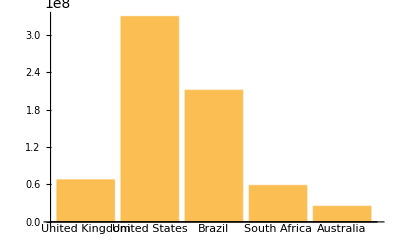

```mathematica
BarChart[popsNow,ChartLabels->countries]
```

By default, the BarChart command generates a vertical bar chart. In straight comparisons like this, a horizontal bar chart is usually preferred:

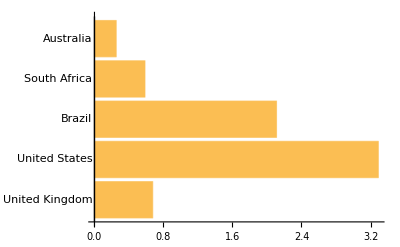

```mathematica
BarChart[popsNow,ChartLabels->countries,BarOrigin->Left]
```

You can add titles and axis labels to your plots:

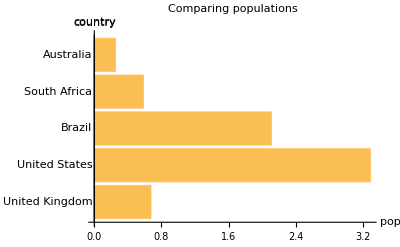

```mathematica
BarChart[popsNow,ChartLabels->countries,BarOrigin->Left,
	PlotLabel->"Comparing populations",
	AxesLabel->{"country","pop"}]
```

Here we can make the horizontal axis easier to read by expressing the population in millions:

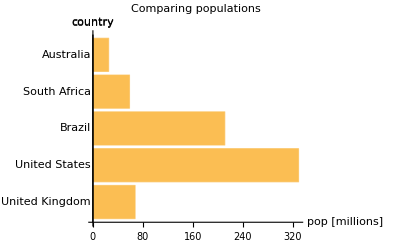

```mathematica
BarChart[popsNow/1000000, ChartLabels->countries,
	BarOrigin->Left,
	PlotLabel->"Comparing populations",
	AxesLabel->{"country","pop [millions]"}]
```

Bar charts are also used to compare changes in some quantity. For example, we can compare the current population to the population in 1950, and assess how population growth differs across these countries. First, let us get the population data for 1950.

```mathematica
pops1950=Map[QuantityMagnitude,
	Map[CountryData[#,{"Population", 1950}]&,
	countriesM]]
```

{50616019,158804397,53974728,13628434,8177348}

Now we plot a bar chart comparing the current population with the population in 1950:

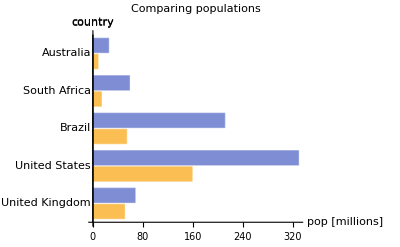

```mathematica
BarChart[Transpose[{pops1950/1000000,
                    popsNow/1000000}], 
	ChartLabels->{countries,None},
	BarOrigin->Left,
	PlotLabel->"Comparing populations",
	AxesLabel->{"country","pop [millions]"}]
```

To understand what is going on here, let us look at this simple example:

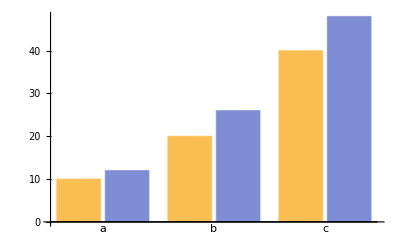

```mathematica
BarChart[{{10,12},{20,26},{40,48}},
	ChartLabels->{{"a","b","c"},None}]
```

The data is grouped into three sets of two data points each. The data given to BarChart is not just a list of numbers as before, it is actually a list of lists. For that reason, the labels passed to the ChartLabels option are not just a plain list of labels as before, but two lists of labels: one for the “outermost” grouping (a, b, c), and one for the “innermost” grouping (denoted by the colours blue and orange). We left this second list of labels blank by giving it the value None, so no label for the innermost grouping is displayed in the plot. Let us try to label the two cases (blue and orange) “1” and “2”:

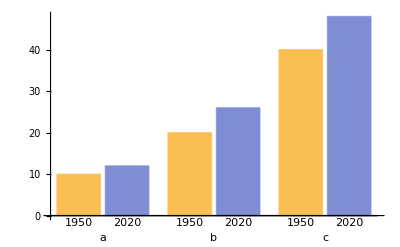

```mathematica
BarChart[{{10,12},{20,26},{40,48}},
	ChartLabels->{{"a","b","c"},{"1950","2020"}}]
```

If we have instead a list of numbers for label “1”, and a list of numbers for label “2”, we use the Transpose function to turn that into a list of pairs, which the BarChart function demands:

```mathematica
Transpose[{{10,20,40},{12,26,48}}]
```

{{10,12},{20,26},{40,48}}

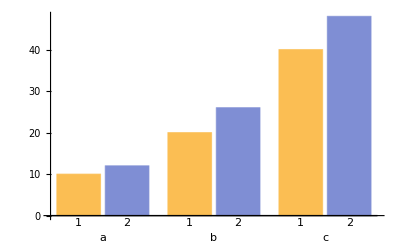

```mathematica
BarChart[Transpose[{{10,20,40},{12,26,48}}],
	ChartLabels->{{"a","b","c"},{"1","2"}}]
```

Using this in our population plot:

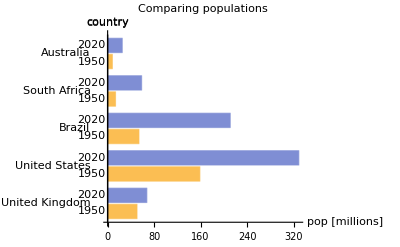

```mathematica
BarChart[Transpose[{pops1950/1000000,popsNow/1000000}], 
	ChartLabels->{countries,{"1950","2020"}},
	BarOrigin->Left,
	PlotLabel->"Comparing populations",
	AxesLabel->{"country","pop [millions]"}]
```

Notice how awkward this is! It is almost never a good idea to label grouped bar charts like this. It is even worse in our original plot of the populations. The information about the year is repeated needlessly for every country. We can use the colour coding instead: blue means 2020 population, orange means 1950 population. Let us put this information in a legend:

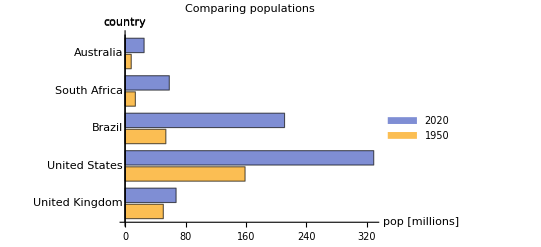

```mathematica
BarChart[Transpose[{pops1950/1000000.0,popsNow/1000000.0}], 
	ChartLabels->{countries,None},
	ChartLegends->{"1950","2020"},
	BarOrigin->Left,
	PlotLabel->"Comparing populations",
	AxesLabel->{"country","pop [millions]"}]
```

### Warning: avoid “fake 3D” charts!

Do not use “fake 3D” charts such as this one:

```mathematica
BarChart3D[popsNow/1000000, ChartLabels->countries,
	PlotLabel->"Don't do this!",
	AxesLabel->{"country","pop [millions]"},
	ImageSize->Medium]
```

-Graphics3D-

The third dimension is used here just to “spice up” the chart, and the result is a plot that feels cluttered and is harder to read. This is just needless clutter, with no upside; don’t do this! Bar charts are intrinsically 2D objects, and you gain nothing by needlessly complicating them in this way.

### Stacked bar charts

Suppose we want to compare not only the total populations of countries, but also see how that population is divided between adults and children. What is the best way to plot that?

First, let us get the data.

```mathematica
popsAdult=Map[QuantityMagnitude,
	Map[CountryData[#,"AdultPopulation"]&,
	countries]];
popsChildren = popsNow - popsAdult
```

{2.55021×10^7,1.15994×10^8,6.64891×10^7,2.18747×10^7,9.31576×10^6}

We could try to use the grouped bar chart, as before:

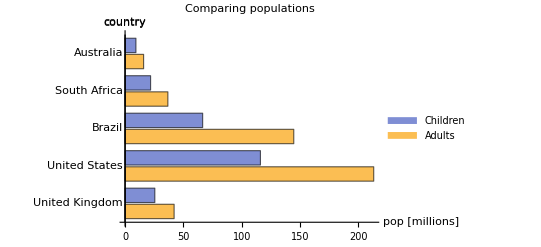

```mathematica
BarChart[Transpose[{popsAdult/1000000.0,
	popsChildren/1000000.0}], 
	ChartLabels->{countries,None},
	ChartLegends->{"Adults","Children"},
	BarOrigin->Left,
	PlotLabel->"Comparing populations",
	AxesLabel->{"country","pop [millions]"}]
```

We can use this plot to compare child to adult population within each country, but we lost the ability to compare populations between different countries. When we have a quantity that is made up of a number of contributions (total population = adults + children), the stacked bar chart is a good choice:

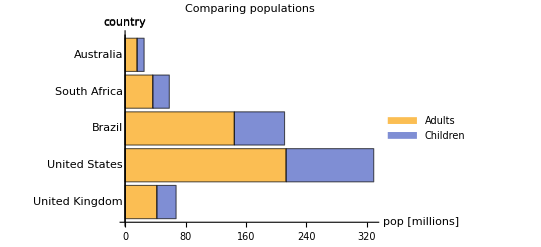

```mathematica
BarChart[Transpose[{popsAdult/1000000.0,
	popsChildren/1000000.0}], 
	ChartLabels->{countries,None},
	ChartLegends->{"Adults","Children"},
	BarOrigin->Left,
	ChartLayout->"Stacked",
	PlotLabel->"Comparing populations",
	AxesLabel->{"country","pop [millions]"}]
```

You now have the ability to compare total populations in different countries, and you can still compare child/adult populations within one country. You also can easily compare adult populations across different countries, but it is more difficult to compare child populations, because their bars start at different levels. 

A variation of the stacked bar chart is useful when you want to compare proportions of quantities. Using our example of adult/child populations, we may want to compare and contrast the proportions of adults versus children across countries. In this case, we do not care about the total population, but about how each population is divided into adults and children. The percentile stacked bar chart works like the usual stacked bar chart, but it forces the total heights of all bars to be the same:

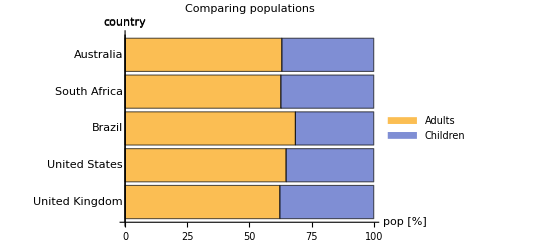

```mathematica
BarChart[Transpose[{popsAdult/1000000.0,
	popsChildren/1000000.0}], 
	ChartLabels->{countries,None},
	ChartLegends->{"Adults","Children"},
	BarOrigin->Left,
	ChartLayout->"Percentile",
	PlotLabel->"Comparing populations",
	AxesLabel->{"country","pop [%]"}]
```

A stacked bar chart consisting of a single bar is useful when you want to depict how some quantity is made up of sub-quantities. To exemplify this, here is some data on the current composition of the UK’s House of Commons:

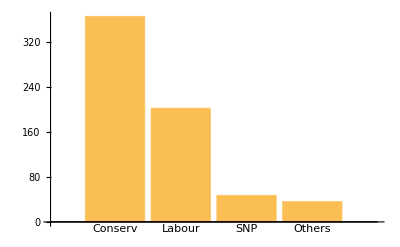

```mathematica
BarChart[ukPartiesNums,ChartLabels->ukParties]
```

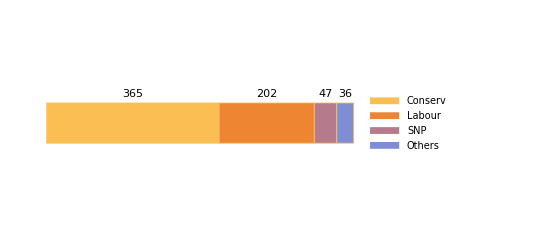

```mathematica
ukParties={"Conserv","Labour","SNP","Others"};
ukPartiesNums={365,202,47,36};
BarChart[ukPartiesNums,
	LabelingFunction->Above,
    ChartLegends->ukParties,
	BarOrigin->Left,
	ChartLayout->"Stacked",
	Axes->None]
```

#### Warning: avoid the pie chart!

A popular way to do what we did with the one-bar stacked bar chart above is using a pie chart:

```mathematica
PieChart[ukPartiesNums,
    ChartLegends->ukParties,
	PlotLabel->"UK parliament",
	ImageSize->Small]
```

-Graphics-

Pie charts are inherently harder to read than the stacked bar chart that does the same job: the proportions of the different quantities in a pie chart are proportional to the perimeter of an arc of a circle, compared to the length of a straight line in the case of the stacked bar chart.

### The scatter plot

Scatter plots are a good way to visualise how two numerical quantities are related to each other. In contrast to bar charts, scatter plots are used for purely numerical quantities, not categorical data. For example, temperature and pressure at a given location; or inflation and average income of some country. Scatter plots are especially useful for finding correlations between quantities.

In their simplest form, a scatter plot is defined for two numerical quantities. To exemplify, let us use the wealth, as measured by the GDP per capita, and the literacy rate, of the set of all countries for which these quantities are recorded in Mathematica’s database:

```mathematica
Transpose[{{1,2,3}, {2,3,4}}]
```

{{1,2},{2,3},{3,4}}

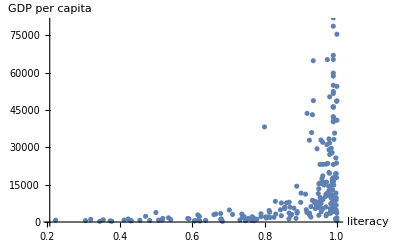

```mathematica
countriesM = CountryData["Countries"];
literacy = Map[CountryData[#, "LiteracyFraction"]&, countriesM];
wealth = Map[CountryData[#, "GDPPerCapita"]&, countriesM];
ListPlot[Transpose[{literacy,wealth}],
    AxesLabel->{"literacy","GDP per capita"}]
```

The Transpose command inside ListPlot creates a list of pairs of the form {literacy,wealth}, which is the form that ListPlot needs. To remind yourself how it works, examine this simple example:

```mathematica
Transpose[{{1,2,3}, {4,5,6}}]
```

{{1,4},{2,5},{3,6}}

We can see from the plot that literacy is indeed correlated to wealth: all countries with GDP per capita greater than 40k have literacy close to 1. However, this connection is not so straightforward: high wealth implies high literacy, but the reverse is not true! There are many countries with high literacy and low wealth (those are the points near the lower-right corner of the plot). Notice that there are no points on the upper-left corner: no countries with high wealth have low literacy.

The wealth varies enormously from country to country. When you are plotting a variable with values that range over many orders of magnitude, it is often a good idea to use a logarithmic scale for the axis of that variable:

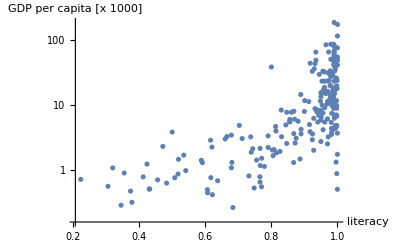

```mathematica
ListLogPlot[Transpose[{literacy, wealth/1000.0}],
	AxesLabel->{"literacy","GDP per capita [x 1000]"}]
```

The logarithmic plot “unpacks” the points, and allows you to get a better view of how they are distributed.

#### Using functions to encapsulate and generalise useful plots

What is we want to make a scatter plot of literacy versus mortality rate? or mortality rate versus inflation? It is very common when you are exploring data to want to plot many variations of the same kind of plot.

The way we created our scatter plot was very “dirty”. We defined lots of little variables to hold the results of temporary computations, polluting the namespace, and we did lots of repetitive coding. To remind you:

```mathematica
countriesM = CountryData["Countries"];
literacy = Map[CountryData[#, "LiteracyFraction"]&, countriesM];
wealth = Map[CountryData[#, "GDPPerCapita"]&, countriesM];
ListPlot[Transpose[{literacy,wealth}],
    AxesLabel->{"literacy","GDP per capita"}]
```

-Graphics-

If we want to plot mortality rate versus inflation, we would need to repeat most of this, creating variables mortality, inflation, etc. Surely there is a way to automate out all this drudgery!

Indeed there is a way: we can create a function that makes the scatter plot for any two given quantities. Here is a first version:

```mathematica
countryPlot[xname_,yname_] := Module[
	{countriesM, x, y},
	
	countriesM = CountryData["Countries"];
	x = Map[CountryData[#, xname]&, countriesM];
	y = Map[CountryData[#, yname]&, countriesM];
	
	ListPlot[Transpose[{x, y}]]
]
```

Let us see if we can recover our original plot using this function:

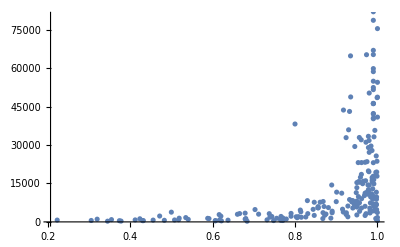

```mathematica
countryPlot["LiteracyFraction", "GDPPerCapita"]
```

It works! However, if we try to set the axis labels, something goes wrong:

```mathematica
countryPlot["LiteracyFraction", "GDPPerCapita",
	AxesLabel->{"literacy","GDP per capita"}]
```

countryPlot[LiteracyFraction,GDPPerCapita,AxesLabel→{literacy,GDP per capita}]

Nothing happens, because our function countryPlot does not know what to do with the AxesLabel option. Unlike ListPlot, our function does not accept options. Let us make it accept all options that ListPlot accepts, and pass these options on to ListPlot:

```mathematica
countryPlot[xname_,yname_, 
			opts:OptionsPattern[ListPlot]] := Module[
	{countriesM, x, y},
	
	countriesM = CountryData["Countries"];
	x = Map[CountryData[#, xname]&, countriesM];
	y = Map[CountryData[#, yname]&, countriesM];
	
	ListPlot[Transpose[{x, y}], opts]
]
```

```mathematica
countryPlot["LiteracyFraction", "GDPPerCapita",
	AxesLabel->{"literacy","GDP per capita"}]
```

-Graphics-

So how is the death rate related to inflation?

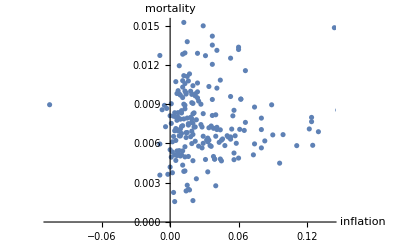

```mathematica
countryPlot["InflationRate", "DeathRateFraction",
	AxesLabel->{"inflation","mortality"}]
```

Now we can use countryPlot to quickly explore the relationship between many quantities. Use the command CountryData[“Properties”] to see which quantities are available in Mathematica’s country database.

### Scatter plots with multiple datasets

We can plot multiple data sets in the same scatterplot using ListPlot or ListLogPlot. So let us divide our set of countries into European and non-European, and plot each set with a different colour. This way we will be able to see where European countries are located in the plot.

```mathematica
european = Select[countriesM, SameQ[CountryData[#,"Continent"],
					 EntityClass["Country","Europe"]]&];
euLiteracy = Map[CountryData[#, "LiteracyFraction"]&, european];
euWealth = Map[CountryData[#, "GDPPerCapita"]&, european];

noneuCountries = Complement[countriesM,european];
noneuCountries = Select[countriesM, Not@SameQ[CountryData[#,"Continent"],
					 EntityClass["Country","Europe"]]&];
noneuLiteracy = Map[CountryData[#, "LiteracyFraction"]&, noneuCountries];
noneuWealth = Map[CountryData[#, "GDPPerCapita"]&, noneuCountries];
```

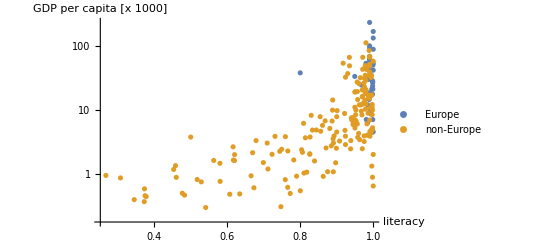

```mathematica
ListLogPlot[{Transpose[{euLiteracy, euWealth/1000.0}],
			 Transpose[{noneuLiteracy, noneuWealth/1000.0}]},
	PlotLegends->{"Europe","non-Europe"},
	AxesLabel->{"literacy","GDP per capita [x 1000]"}]
```

#### Using tooltips

The problem with our scatter plots is that we cannot tell which country each point represents. We will solve this problem by using tooltips instead of plain data.

To see how this works, let us start with the following very simple scatter plot:

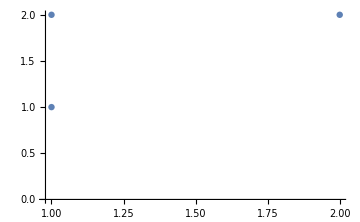

```mathematica
ListPlot[{{1,1}, {2,2}, {1,2}}, ImageSize->Medium]
```

Now we wrap up one of the points by a tooltip:

```mathematica
ListPlot[{{1,1}, Tooltip[{2,2},"this is a tip"], {1,2}}, ImageSize->Medium]
```

-Graphics-

Now if you hover the mouse over the point {2,2}, a tooltip with the text “this is a tip” will appear. We can do this for every point, with customized text for each point:

```mathematica
ListPlot[Map[Tooltip[#,Row[{"x=",#[[1]], " y=,",#[[2]]}]]&,
	{{1,1}, {2,2}, {1,2}}], ImageSize->Medium]
```

-Graphics-

Now we want to do something similar with our scatter plot of countries. The tooltip message should be the name of the country, so that by moving the mouse over a point we can learn what country it represents:

```mathematica
countriesM = CountryData["Countries"];
literacy = Map[CountryData[#, "LiteracyFraction"]&, countriesM];
wealth = Map[CountryData[#, "GDPPerCapita"]&, countriesM];

ttipData = Transpose[{literacy, wealth/1000.0, countriesM}];
ttipPts = Map[Tooltip[{#⟦1⟧, #⟦2⟧}, #⟦3⟧]&, ttipData];
ListLogPlot[ttipPts,
	AxesLabel->{"literacy","GDP per capita [x 1000]"}]
```

-Graphics-

Now if when your mouse goes over a country, its name will pop up in a tooltip. This is our first example of making a plot interactive, and it is just the tip of the iceberg. We will have much more to say about this in the near future.

#### Multiple plots

It is often useful to have a grid of similar charts displayed on the same plot (this may take a few minutes to plot):

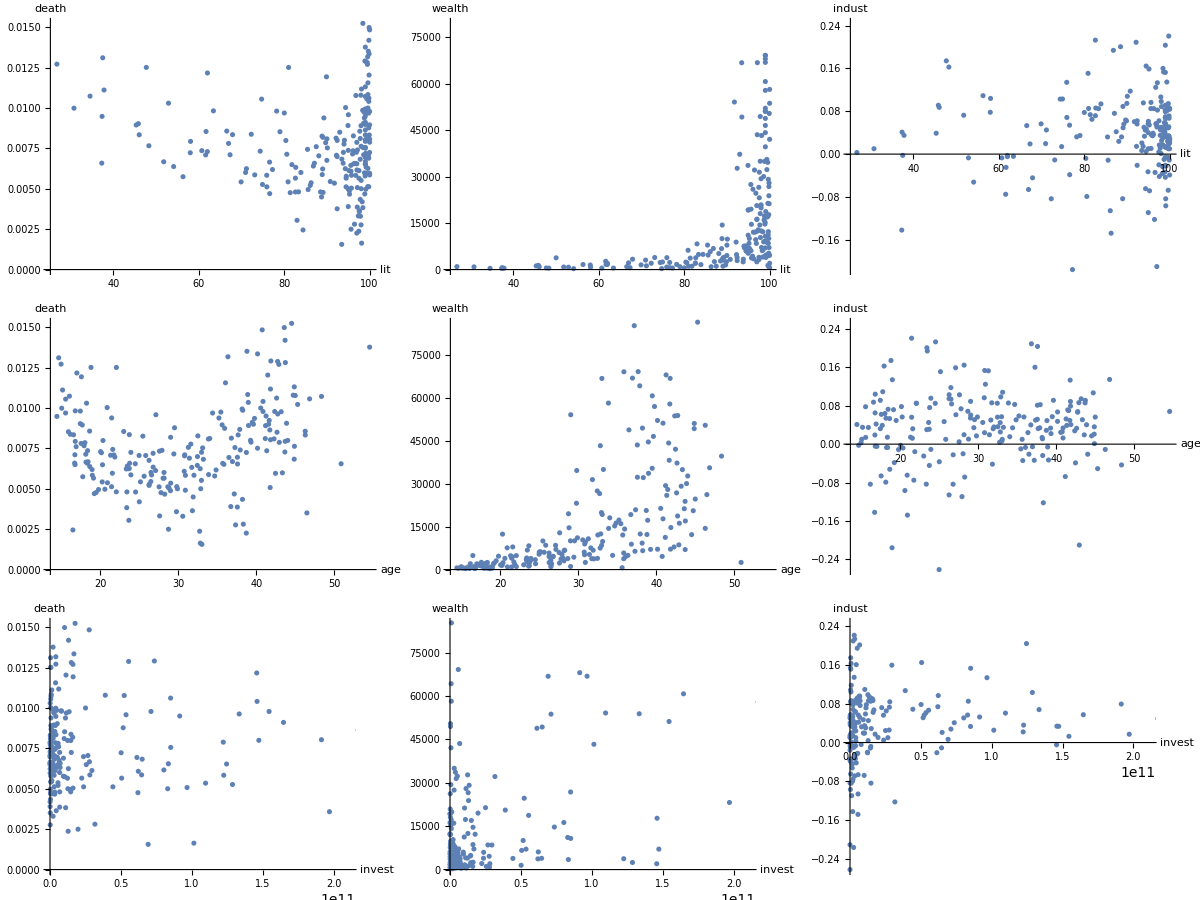

```mathematica
xs = {"LiteracyRate", "MedianAge","GrossInvestment"};
xsShort = {"lit", "age", "invest"};
ys = {"DeathRateFraction", "GDPPerCapita", 
	"IndustrialProductionGrowth"};
ysShort = {"death", "wealth", "indust"};
Grid@Table[countryPlot[xs⟦m⟧, ys⟦n⟧,
	AxesLabel->{xsShort⟦m⟧, ysShort⟦n⟧}],
	{m, 1, 3}, {n, 1, 3}]
```

This does not look very good! The axis labels are getting in the way, making the plots hard to read. One solution is to get rid of the axes altogether:

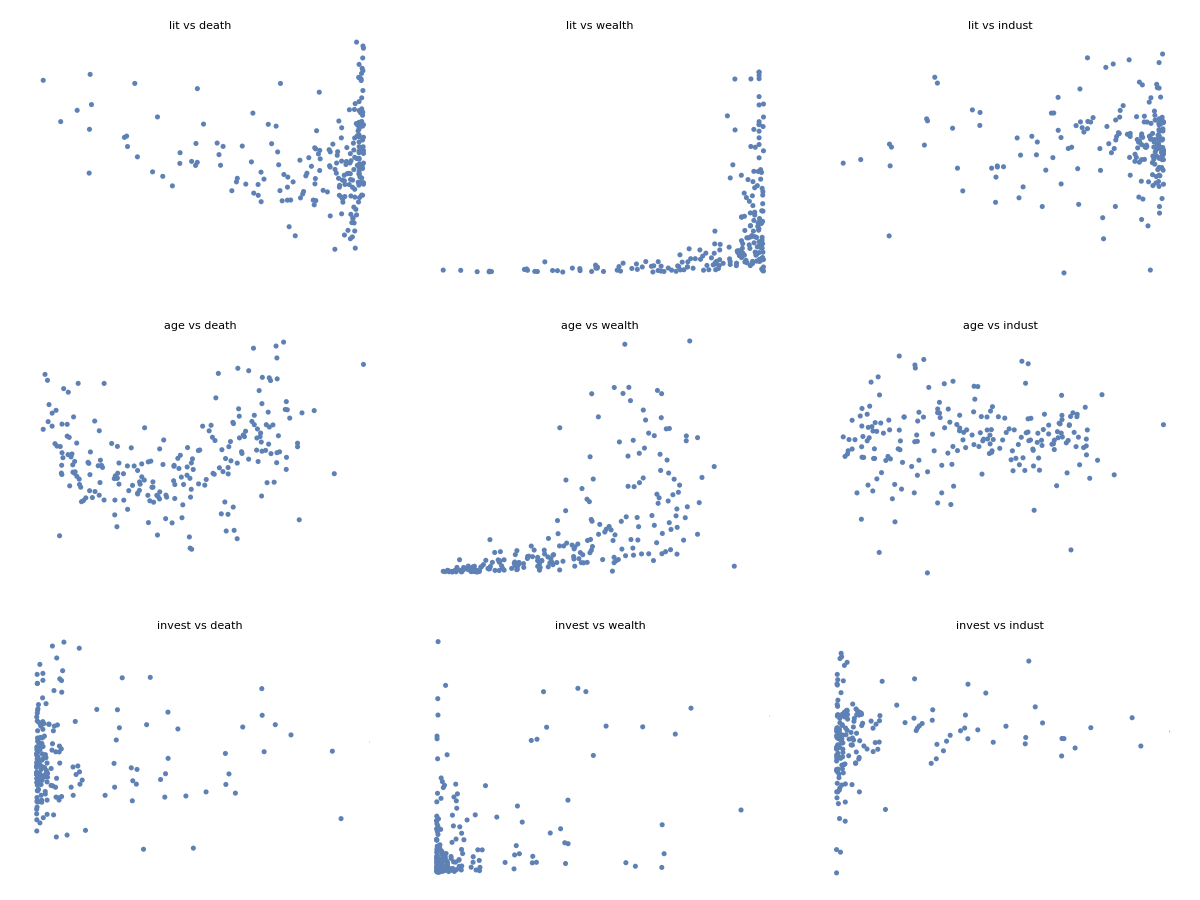

```mathematica
Grid[Table[countryPlot[xs⟦m⟧, ys⟦n⟧,
	PlotLabel->Row[{xsShort⟦m⟧, " vs ", ysShort⟦n⟧}],
	Axes->None],
	{m, 1, 3}, {n, 1, 3}], Frame->All]
```

This allows us to assess the correlations between the variables without being burdened with spurious graphical elements.

An alternative way to visualise a set of charts is to use a TabView:

```mathematica
TabView[Table[countryPlot["LiteracyRate", ys⟦n⟧,
			  AxesLabel->{"lit", ysShort⟦n⟧}],
			  {n, 1, 3}]]
```

123

We can label each tab by associating the label with the corresponding plot:

```mathematica
TabView[Table[ysShort⟦n⟧->countryPlot["LiteracyRate", ys⟦n⟧,
			  AxesLabel->{"lit", ysShort⟦n⟧}],
			  {n, 1, 3}]]
```

123

## Line plots

In line plots, data points are laid out in a linear sequence. The most common application of line plots is to show how some quantity is changing over time:

```mathematica
ListLinePlot[Transpose[{years,worldPop}],ImageSize->Medium,
	AxesLabel->{"year","population"},
	PlotLabel->"World population over time"]
```

-Graphics-

The sequence of points is usually shown by connecting the data points by a line (hence the term “line plot”). You could also show the symbols to emphasize where the data points are:

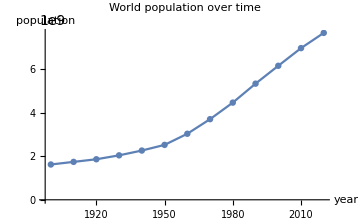

```mathematica
ListPlot[Transpose[{years,worldPop}],ImageSize->Medium,
	Joined->True, Mesh->All,
	AxesLabel->{"year","population"},
	PlotLabel->"World population over time"]
```

Sometimes, we may even not show lines at all:

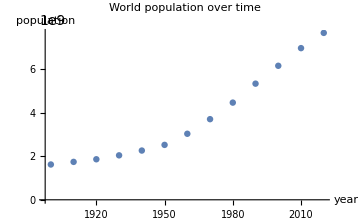

```mathematica
ListPlot[Transpose[{years,worldPop}],ImageSize->Medium,
	AxesLabel->{"year","population"},
	PlotLabel->"World population over time"]
```

Despite the fact that there are no lines, we still call this a “line plot”. The important thing is that the data points are in a sequence, from earlier times to later times in this case.

Line plots are the preferred way to show change over time. In general, they are used to show how some quantity depends on another quantity:

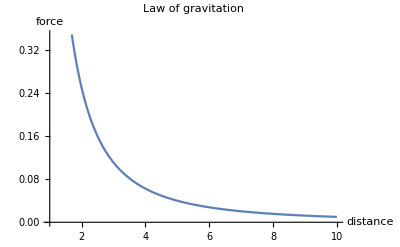

```mathematica
Plot[1/r^2,{r, 1, 10}, 
	PlotLabel->"Law of gravitation",
	AxesLabel->{"distance","force"}]
```

Plotting the same quantity for multiple entities is a good way to compare changes over time:

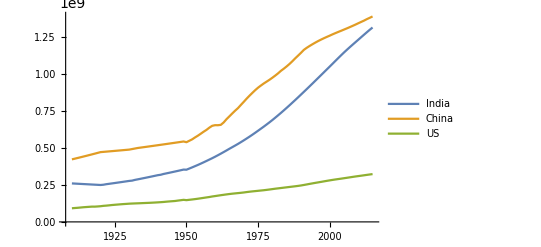

```mathematica
popIndia = Table[{y,CountryData["India", {{"Population"},y}]},
                 {y, 1910,2015}];
popChina = Table[{y,CountryData["China", {{"Population"},y}]},
                 {y, 1910,2015}];
popUS = Table[{y,CountryData["UnitedStates", {{"Population"},y}]},
                 {y, 1910,2015}];

ListLinePlot[{popIndia, popChina, popUS}, PlotLegends->{"India", "China", "US"}]
```

Just by looking at this plot, we can tell that the population growth in these countries accelerated around the 1950s; that the US population has grown much more slowly than the other two; and that the growth of China’s population had a noticeable decrease in the mid-1990s.

Let us compare the wealth of these three countries:

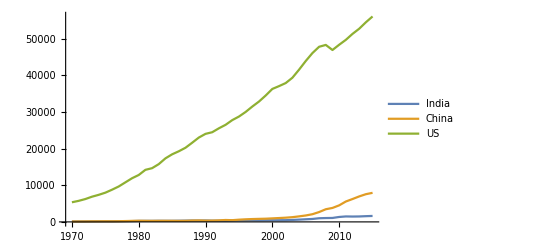

```mathematica
wealthIndia = Table[{y,CountryData["India", {{"GDPPerCapita"},y}]},
                 {y, 1910,2015}];
wealthChina = Table[{y,CountryData["China", {{"GDPPerCapita"},y}]},
                 {y, 1910,2015}];
wealthUS = Table[{y,CountryData["UnitedStates", {{"GDPPerCapita"},y}]},
                 {y, 1910,2015}];
ListLinePlot[{wealthIndia, wealthChina, wealthUS}, 
             PlotLegends->{"India", "China", "US"}]
```

Notice that the plot starts in 1960; earlier data is not available through CountryData. The US’s wealth has increased steadily, particularly from the mid-1970s, while the other two countries seem to have stayed at low levels until the 2000s, when China’s wealth shoots up, and India’s increases as well. Notice the slump in the US’s wealth, just before 2010. Any guesses about the cause of this?

Because of the tremendous disparity in the values, it is worth plotting this using a logarithmic scale for the vertical axis:

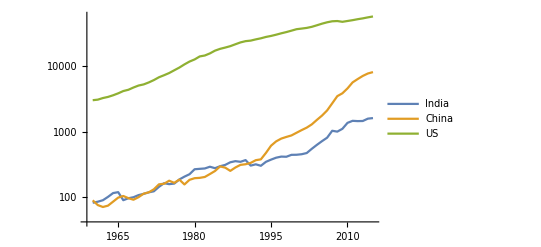

```mathematica
ListLogPlot[{wealthIndia, wealthChina, wealthUS},
			Joined->True,
            PlotLegends->{"India", "China", "US"}]
```

With the logarithmic scale, we see that in fact the India’s and China’s wealth has in fact increased since the 1960’s, but this increase was hidden by the scale of the previous plot. This is an important lesson: changes in quantities may not be visible in a plot if the scales are not chosen properly.

Notice, on the other hand, that the decrease in the US’s wealth is barely visible in the logarithmic plot!

Another way you could have visualised the changes in wealth for India and China is by not plotting the US’s data on the same graph:

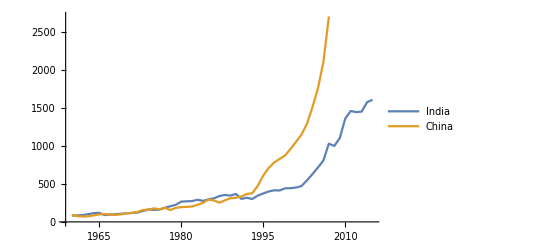

```mathematica
ListLinePlot[{wealthIndia, wealthChina}, 
             PlotLegends->{"India", "China"}]
```

The changes become more clear, because the lines for India and China are not squashed by the presence of the much higher US values.

Another important point to consider when interpreting line plots is the data resolution. Let us plot the same wealth data, but at 5-year intervals:

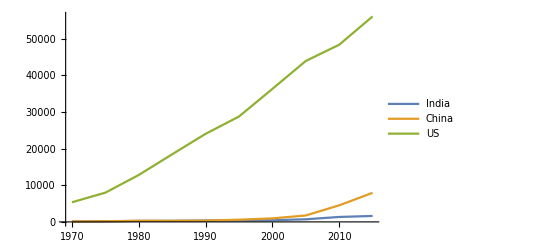

```mathematica
wealthIndia = Table[{y,CountryData["India", {{"GDPPerCapita"},y}]},
                 {y, 1910,2015,5}];
wealthChina = Table[{y,CountryData["China", {{"GDPPerCapita"},y}]},
                 {y, 1910,2015,5}];
wealthUS = Table[{y,CountryData["UnitedStates", {{"GDPPerCapita"},y}]},
                 {y, 1910,2015,5}];
ListLinePlot[{wealthIndia, wealthChina, wealthUS},
             PlotLegends->{"India", "China", "US"}]
```

The slump in the US data all but disappeared! This is something to remember when interpreting your data using line plots.

If you have two different quantities changing over time (for example, population and wealth), laying two line plots vertically so that their axes are aligned is a good way to compare how the two quantities and see if their changes are related:

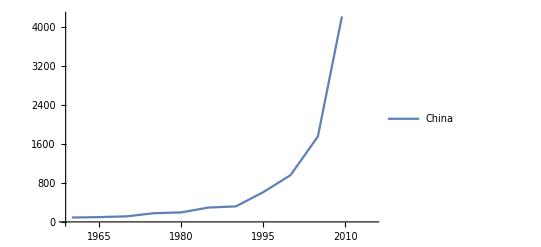
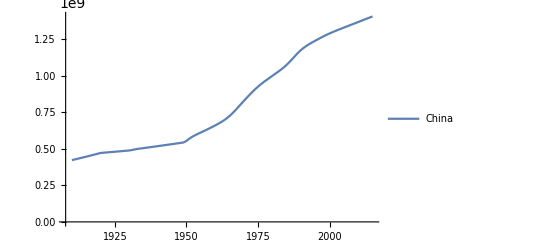

```mathematica
Column[{ListLinePlot[wealthChina, 
             PlotLegends->{"China"}],
        ListLinePlot[popChina, 
             PlotLegends->{"China"}]}]
```

This first attempt does not work for two reasons: the vertical axes do not cover the same range; and the vertical axes labeling is messing up the alignment. Let us fix these issues:

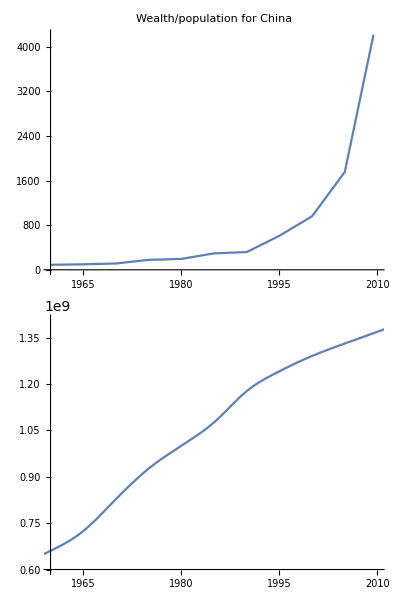

```mathematica
Column[{ListLinePlot[wealthChina,
             PlotRange->{{1960,2010},Automatic},
             Axes->{Automatic,None},
             PlotLabel->"Wealth/population for China"],
        ListLinePlot[popChina, 
             PlotRange->{{1960,2010},{600000000,Automatic}},
             Axes->{Automatic,None}]}]
```

This plot makes it clear that the sudden acceleration in the growth of wealth in China happened at about the same time as the population growth slowed down.